```mathematica
(********************* PARAMATERS *********************)
```

```mathematica
(*constant rates at bioogical equilibrium*)
kSXeq=kSPeq=kXXPeq=kPXPeq=0.1;
kXSeq=0.8;
kPSeq=2*10^4;
kXPXeq=500;
kXPPeq=2*10^(-2);
P=1000;
(*maximum drive injected on each edge (units of kbT)*)
ΔμATP=20;
(*symbolic parameters*)
rates={kXS,kSX,kSP,kPS,kXPX,kXXP,kXPP,kPXP};
vars={kXS,kSX,kSP,kPS,kXPX,kXXP,kXPP,kPXP,X};
(*plotting parameters*)
color1Inflection=CMYKColor[0.0374,0.119,0.5045,0];
color2Inflections=CMYKColor[0,0.3384,0.5957,0];
color3Inflections=CMYKColor[0,0.4677,0.3603,0];
abounds={{10^(-3),10^(3)},{-10^(30),10^(30)},{10^3,10^8},{1.26,15.8}};
bbounds={{10^(-3),10^(3)},{10^(-30),10^(30)},{10^-0.000000000001,10^0.00000000001},{3.2,15.8}};
Npoints={200,50,60,30};
epsilon=0.9*10^(-30);
```

```mathematica
(********************* COMPUTATION OF THE STEADY STATE PROBABILITIES *********************)
```

```mathematica
(*Transposed of the Lagrangian L, such that dp/dt=Lp, whith p the vector composed of the probabilities of being in each state. The order of the states is S P XP X. *)
```

```mathematica
LagrangianT={
{-kSP*P-kSX*X,kSP*P,0,kSX*X},
{kPS,-kPS-kPXP*X,kPXP*X,0},
{0,kXPP,-kXPP-kXPX,kXPX},
{kXS,0,kXXP*P,-kXS-kXXP*P}
};
LagrangianT//MatrixForm
```

(-1000 kSP-kSX X | 1000 kSP | 0 | kSX X
kPS | -kPS-kPXP X | kPXP X | 0
0 | kXPP | -kXPP-kXPX | kXPX
kXS | 0 | 1000 kXXP | -kXS-1000 kXXP)

```mathematica
p=ContinuousMarkovProcess[{1,0,0,0},LagrangianT];
(*probability of the different states at steady state*)
pS[kXS_,kSX_,kSP_,kPS_,kXPX_,kXXP_,kXPP_,kPXP_,X_]:=PDF[p[∞],1];pP[kXS_,kSX_,kSP_,kPS_,kXPX_,kXXP_,kXPP_,kPXP_,X_]:=PDF[p[∞],2];pXP[kXS_,kSX_,kSP_,kPS_,kXPX_,kXXP_,kXPP_,kPXP_,X_]:=PDF[p[∞],3];pX[kXS_,kSX_,kSP_,kPS_,kXPX_,kXXP_,kXPP_,kPXP_,X_]:=PDF[p[∞],4];

(********************* COMPUTATION of mRNA PRODUCTION AS A FUNCTION OF X : r(x) *********************)

(*production rate of dmRNA*)
rofX=Expand[Numerator[Simplify[(pP[kXS,kSX,kSP,kPS,kXPX,kXXP,kXPP,kPXP,X]+pXP[kXS,kSX,kSP,kPS,kXPX,kXXP,kXPP,kPXP,X])]]]/Expand[Denominator[Simplify[(pP[kXS,kSX,kSP,kPS,kXPX,kXXP,kXPP,kPXP,X]+pXP[kXS,kSX,kSP,kPS,kXPX,kXXP,kXPP,kPXP,X])]]];
r[{kXS_,kSX_,kSP_,kPS_,kXPX_,kXXP_,kXPP_,kPXP_,X_}]:=Evaluate[(rofX/. Thread[vars->vars])];
```

```mathematica
(********************* COMPUTATION of dr/dX : dr(X) *********************)
```

```mathematica
drofX=FullSimplify[D[r[{kXS,kSX,kSP,kPS,kXPX,kXXP,kXPP,kPXP,X}],X]];
dr[{kXS_,kSX_,kSP_,kPS_,kXPX_,kXXP_,kXPP_,kPXP_,X_}]:=Evaluate[(drofX/. Thread[vars->vars])];
```

```mathematica
(********************* FUNCTIONNAL FORM OF mRNA PRODUCTION r(X) = (A0 + B0 X + C0 X^2)/(D0 + E0 X + F0 X^2) *********************)
(* computation of the coefficients A0, B0, C0, D0, E0,F0 *)
```

```mathematica
A0=Coefficient[Expand[Numerator[r[{kXS,kSX,kSP,kPS,kXPX,kXXP,kXPP,kPXP,X}]]],X,0];
B0=Coefficient[Expand[Numerator[r[{kXS,kSX,kSP,kPS,kXPX,kXXP,kXPP,kPXP,X}]]],X,1];
C0=Coefficient[Expand[Numerator[r[{kXS,kSX,kSP,kPS,kXPX,kXXP,kXPP,kPXP,X}]]],X,2];
D0=Coefficient[Expand[Denominator[r[{kXS,kSX,kSP,kPS,kXPX,kXXP,kXPP,kPXP,X}]]],X,0];
E0=Coefficient[Expand[Denominator[r[{kXS,kSX,kSP,kPS,kXPX,kXXP,kXPP,kPXP,X}]]],X,1];
F0=Coefficient[Expand[Denominator[r[{kXS,kSX,kSP,kPS,kXPX,kXXP,kXPP,kPXP,X}]]],X,2];
```

```mathematica
(********************* NORMALIZED RATE OF mRNA PRODUCTION r̂(x) = (r(X)-r(0))/(r(0)-r(∞))=(a x + x.b2)/(1 + b x + x.b2), x=X/X0 *********************)
```

```mathematica
(*non dimensionalisation by X0=√(D0/F0)*)
```

```mathematica
(*coefficient b=E0 √(1/(F0 D0)) and a=√(F0/D0) (B0 D0 - A0 E0)/(C0 D0 - A0 F0)*)
```

```mathematica
coefficientb=FullSimplify[E0/Sqrt[(F0*D0)]];
coefficienta=FullSimplify[Sqrt[(F0/D0)]*(B0*D0-A0*E0)/(C0*D0-A0*F0)];
b[{kXS_,kSX_,kSP_,kPS_,kXPX_,kXXP_,kXPP_,kPXP_}]:=Evaluate[(coefficientb/. Thread[rates->rates])];
a[{kXS_,kSX_,kSP_,kPS_,kXPX_,kXXP_,kXPP_,kPXP_}]:=Evaluate[(coefficienta/. Thread[rates->rates])];
```

```mathematica
(********************* MINIMAL AND MAXIMAL BOUNDS FOR COEFFICIENT b *********************)
```

```mathematica
(* Coefficients a and b are functions of the rate constants. We find the maxmimum of b, on the set [Exp[-ΔμATP]kXSeq,Exp[ΔμATP]kXSeq]x[Exp[-ΔμATP]kSXeq,Exp[ΔμATP]kSXeq]x[Exp[-ΔμATP]kSPeq,Exp[ΔμATP]kSPeq]x[Exp[-ΔμATP]kPSeq,Exp[ΔμATP]kPSeq]x[Exp[-ΔμATP]kXPXeq,Exp[ΔμATP]kXPXeq]x[Exp[-ΔμATP]kXXPeq,Exp[ΔμATP]kXXPeq]x[Exp[-ΔμATP]kXPPeq,Exp[ΔμATP]kXPPeq]x[Exp[-ΔμATP]kPXPeq,Exp[ΔμATP]kPXPeq]. The coefficient a is not bounded on this set and can take any real value. *)
```

```mathematica
log10bmax=FindMaximum[{Log10[b[{kXSeq*Exp[ Δμ1],kSXeq *Exp[ Δμ2],kSPeq *Exp[ Δμ3],kPSeq *Exp[ Δμ4],kXPXeq *Exp[ Δμ5],kXXPeq*Exp[ Δμ6],kXPPeq *Exp[ Δμ7],kPXPeq *Exp[ Δμ8]}]],ΔμATP≥Δμ1≥-ΔμATP,ΔμATP≥Δμ2≥-ΔμATP,ΔμATP≥Δμ3≥-ΔμATP,ΔμATP≥Δμ4≥-ΔμATP,ΔμATP≥Δμ5≥-ΔμATP,ΔμATP≥Δμ6≥-ΔμATP,ΔμATP≥Δμ7≥-ΔμATP,ΔμATP≥Δμ8≥-ΔμATP},{Δμ1,Δμ2,Δμ3,Δμ4,Δμ5,Δμ6,Δμ7,Δμ8},MaxIterations->50000][[1]];
log10bmin=FindMinimum[{Log10[b[{kXSeq*Exp[ Δμ1],kSXeq *Exp[ Δμ2],kSPeq *Exp[ Δμ3],kPSeq *Exp[ Δμ4],kXPXeq *Exp[ Δμ5],kXXPeq*Exp[ Δμ6],kXPPeq *Exp[ Δμ7],kPXPeq *Exp[ Δμ8]}]],ΔμATP≥Δμ1≥-ΔμATP,ΔμATP≥Δμ2≥-ΔμATP,ΔμATP≥Δμ3≥-ΔμATP,ΔμATP≥Δμ4≥-ΔμATP,ΔμATP≥Δμ5≥-ΔμATP,ΔμATP≥Δμ6≥-ΔμATP,ΔμATP≥Δμ7≥-ΔμATP,ΔμATP≥Δμ8≥-ΔμATP},{Δμ1,Δμ2,Δμ3,Δμ4,Δμ5,Δμ6,Δμ7,Δμ8},MaxIterations->50000][[1]];
```

```mathematica
log10bmax
log10bmin
```

20.3718

-6.53529

```mathematica
(********************* EQUILIBRIUM VALUES OF COEFFICIENTS a AND b *********************)
```

```mathematica
aeq=a[{kXSeq,kSXeq,kSPeq,kPSeq,kXPXeq,kXXPeq,kXPPeq,kPXPeq}];
beq=b[{kXSeq,kSXeq,kSPeq,kPSeq,kXPXeq,kXXPeq,kXPPeq,kPXPeq}];
```

```mathematica
aeq
beq
```

173.209

173.214

```mathematica
(********************* CONDITIONS FOR HAVING 1, 2 or 3 INFLECTIONS - dervied in EqS98toS100.nb *********************)
```

```mathematica
Inflection1[a_,b_]:=(0<a<2&&a<b<Root[-1024-1024 a^2+1024 a #1+(-64-64 a^2) #1^2+64 a #1^3+(-28-a^2) #1^4+a #1^5&,1])||(2<a<Root"2.35"Root[-343-1041 #1^2+195 #1^4+#1^6&,2]2.3458097637115753&&(a<b<Root[-1024-1024 a^2+1024 a #1+(-64-64 a^2) #1^2+64 a #1^3+(-28-a^2) #1^4+a #1^5&,1]||Root[-1024-1024 a^2+1024 a #1+(-64-64 a^2) #1^2+64 a #1^3+(-28-a^2) #1^4+a #1^5&,2]<b<Root[-1024-1024 a^2+1024 a #1+(-64-64 a^2) #1^2+64 a #1^3+(-28-a^2) #1^4+a #1^5&,3]))||(a>Root"2.35"Root[-343-1041 #1^2+195 #1^4+#1^6&,2]2.3458097637115753&&a<b<Root[-1024-1024 a^2+1024 a #1+(-64-64 a^2) #1^2+64 a #1^3+(-28-a^2) #1^4+a #1^5&,1])
```

```mathematica
Inflection2[a_,b_]:=(a<0&&0≤b)||(a>0&&0≤b<a)
```

```mathematica
Inflection3[a_,b_]:=b≥0&&(((0<a<2||(a>2&&a<Root"2.35"Root[-343-1041 #1^2+195 #1^4+#1^6&,2]2.3458097637115753&&b<Root[-1024-1024 a^2+1024 a #1+(-64-64 a^2) #1^2+64 a #1^3+(-28-a^2) #1^4+a #1^5&,2])||a>Root"2.35"Root[-343-1041 #1^2+195 #1^4+#1^6&,2]2.3458097637115753)&&b>Root[-1024-1024 a^2+1024 a #1+(-64-64 a^2) #1^2+64 a #1^3+(-28-a^2) #1^4+a #1^5&,1])||(a<Root"2.35"Root[-343-1041 #1^2+195 #1^4+#1^6&,2]2.3458097637115753&&a>2&&b>Root[-1024-1024 a^2+1024 a #1+(-64-64 a^2) #1^2+64 a #1^3+(-28-a^2) #1^4+a #1^5&,3]))
```

```mathematica
(********************* RELATION WITH a AND b AT EQUILIBRIUM *********************)
```

```mathematica
(* at detailed balance, the system is constrained because γ=(kSX kXXP kXPP kPS)/(kXS kXPX kPXP kSP), there is a relation between a and b*)
bAtEq[a_]:=a+1/a
```

```mathematica
(********************* PLOTS *********************)
```

```mathematica
(* in the (a,b) space we can distinguish three regions, the region where the fold change has 1, 2 or 3 inflection. We reprent this space hereafter. The blue line are the bounds of b that can be reached for dmRNA=pbound=pP+pXP. The black line is detailed balance. The black dot is the biological equilibrium that is found in the litterature (aeq,beq). *)
```

```mathematica
Plot1=Show[{RegionPlot[{Inflection1[a,b],Inflection2[a,b],Inflection3[a,b]},{a,abounds[[1]][[1]],abounds[[1]][[2]]},{b,bbounds[[1]][[1]],bbounds[[1]][[2]]},Frame->True,FrameLabel->{"a","b"},PlotLegends->{"inflection1","inflection2","inflection3"},PlotStyle->{{Opacity[1],color1Inflection},{Opacity[1],color2Inflections},{Opacity[1],color3Inflections}},BoundaryStyle->{1->color1Inflection,2->color2Inflections,3->color3Inflections},Mesh->None,ScalingFunctions->{"Log","Log"},AspectRatio->1,PlotPoints->{Npoints[[1]],Npoints[[1]]}],Plot[bAtEq[a],{a,abounds[[1]][[1]],abounds[[1]][[2]]},PlotStyle->{Black},PlotLegends->{"Detail Balance"},ScalingFunctions->{"Log","Log"}],Graphics[{PointSize[0.03],Black,Point[{Log10[aeq],Log10[beq]}]}]}]
```

-Graphics-

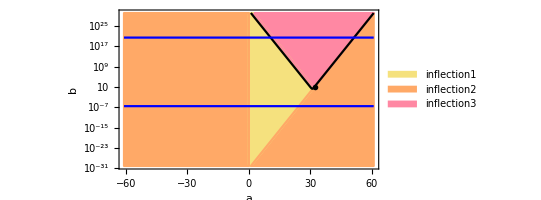

```mathematica
Plot2=Show[{RegionPlot[{Inflection1[a,b],Inflection2[a,b],Inflection3[a,b]},{a,abounds[[2]][[1]],abounds[[2]][[2]]},{b,bbounds[[2]][[1]],bbounds[[2]][[2]]},FrameLabel->{"a","b"},PlotLegends->{"inflection1","inflection2","inflection3"},PlotStyle->{{Opacity[1],color1Inflection},{Opacity[1],color2Inflections},{Opacity[1],color3Inflections}},BoundaryStyle->{1->color1Inflection,2->color2Inflections,3->color3Inflections},Mesh->None,ScalingFunctions->{{"SignedLog",epsilon},"Log"},AspectRatio->1/2],Plot[bAtEq[a],{a,epsilon,abounds[[2]][[2]]},PlotStyle->{Black},PlotLegends->{"Detail Balance"},ScalingFunctions->{{"SignedLog",epsilon},"Log"}],Plot[{10^log10bmin,10^log10bmax},{a,abounds[[2]][[1]],abounds[[2]][[2]]},PlotStyle->{Blue},PlotLegends->{"bmin","bmax"},ScalingFunctions->{{"SignedLog",epsilon},"Log"}],Graphics[{PointSize[0.01],Black,Point[{Log10[aeq]-Log10[epsilon],Log10[beq]}]}]}]
```

```mathematica
(*zoom along the diagonal b=a, this shows that there is a thin rubbon between the 2 and 3 inflections zones in which the fold change has one inflection. The detailed balance curve is in this zone. To zoom on the diagonal, we rotate the figure of 45° and plot (b/a) with respect to a*)
```

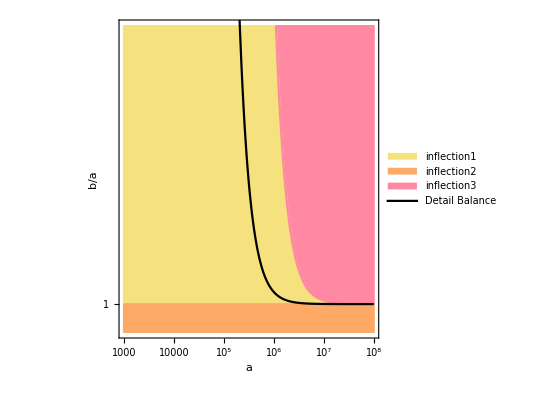

```mathematica
Plot3=Show[{RegionPlot[{Inflection1[a,a*b],Inflection2[a,a*b],Inflection3[a,a*b]},{a,abounds[[3]][[1]],abounds[[3]][[2]]},{b,bbounds[[3]][[1]],bbounds[[3]][[2]]},FrameLabel->{"a","b/a"},PlotLegends->{"inflection1","inflection2","inflection3"},PlotPoints->{Npoints[[3]],Npoints[[3]]},PlotStyle->{{Opacity[1],color1Inflection},{Opacity[1],color2Inflections},{Opacity[1],color3Inflections}},BoundaryStyle->{1->color1Inflection,2->color2Inflections,3->color3Inflections},Mesh->None,ScalingFunctions->{"Log","Log"}],Plot[bAtEq[a]/a,{a,abounds[[3]][[1]],abounds[[3]][[2]]},PlotStyle->{Black},PlotLegends->{"Detail Balance"},ScalingFunctions->{"Log","Log"}]}]
```

```mathematica
(*zoom on the tip - we see there is no 'triple point' and more details of the shape of this tip*)
```

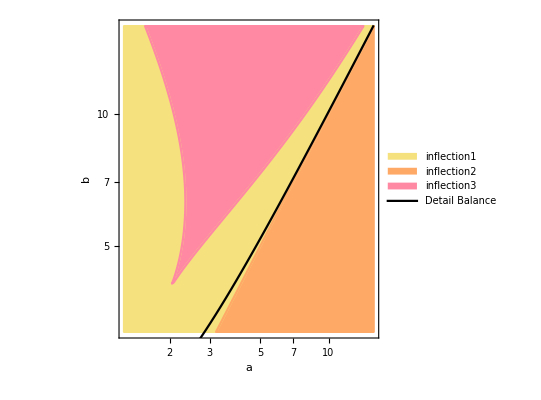

```mathematica
Plot4=Show[{RegionPlot[{Inflection1[a,b],Inflection2[a,b],Inflection3[a,b]},{a,abounds[[4]][[1]],abounds[[4]][[2]]},{b,bbounds[[4]][[1]],bbounds[[4]][[2]]},FrameLabel->{"a","b"},PlotLegends->{"inflection1","inflection2","inflection3"},PlotPoints->{Npoints[[4]],Npoints[[4]]},Mesh->None,PlotStyle->{{Opacity[1],color1Inflection},{Opacity[1],color2Inflections},{Opacity[1],color3Inflections}},BoundaryStyle->{1->color1Inflection,2->color2Inflections,3->color3Inflections},ScalingFunctions->{"Log","Log"}],Plot[bAtEq[a],{a,abounds[[4]][[1]],abounds[[4]][[2]]},PlotStyle->{Black},PlotLegends->{"Detail Balance"},ScalingFunctions->{"Log","Log"}]}]
```

```mathematica
□_□
```

□_□